# Magnus Effect

#### 2D Motion with the drag

```mathematica
SetDirectory[NotebookDirectory[]];
ρ=1.2;(*kg/m^3, air density*)
R = 0.0125; (* radius *)
Subscript[C, D]=1.17;(* drag coefficient *)
TurbulentDrag[v_]:=-1/2 ρ v^2 Subscript[C, D] A ;(* if turbulent drag is used *)

A = π R^2; (*crossection area*)
m = 0.01 ;(*10g*)
g = -9.8; 
 (*_____________________________*)
V[vx_, vy_]:=Sqrt [vx^2+vy^2];
CosAlpha[vx_, vy_] :=vx/V[vx, vy];
SinAlpha[vx_, vy_] :=vy/V[vx, vy];
(*_____________________________*)
Tmax = 1.5;

sFree=NDSolve[{
m* x''[t]==0,
m* y''[t]==m g ,
x[0] == 0, x'[0]==5, y[0]==0, y'[0]==0},{x,y}, {t,0,Tmax}];

sT=NDSolve[{
m* x''[t]==TurbulentDrag[V[x'[t], y'[t]]]*CosAlpha[x'[t], y'[t]],
m* y''[t]==m g + TurbulentDrag[V[x'[t], y'[t]]]*SinAlpha[x'[t], y'[t]],
x[0] == 0, x'[0]==5, y[0]==0, y'[0]==0},{x,y}, {t,0,Tmax}];
```

```mathematica
pF = ParametricPlot[
Evaluate[{x[t],y[t]}/.sFree],
{t,0,Tmax},
AxesLabel->{"x coordinate, m", "y coordinate, m"},
PlotLabel -> "Trajectory of motion in 2D with drag", 
AspectRatio->Automatic, 
PlotStyle-> Blue];

pD = ParametricPlot[
Evaluate[{x[t],y[t]}/.sT],
{t,0,Tmax},
AxesLabel->{"x coordinate, m", "y coordinate, m"},
PlotLabel -> "Trajectory of motion in 2D", 
AspectRatio->Automatic, PlotStyle->{Dashed, Red}];

Show[pF, pD];
```

#### Add Magnus effect (using cylinder as an object)

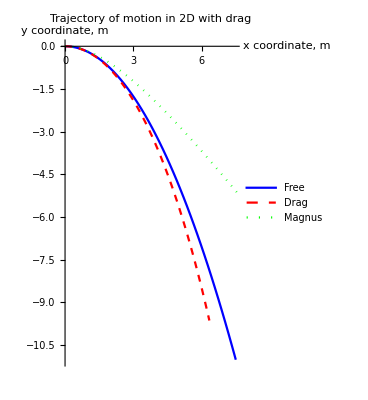

```mathematica
L = 0.2; (*cylinder length*)
r = 0.02; (*cylinder radius *)
ω=10; (*assume it is a constant during motion, for a first approximation *)
(*Students have carefully consider sign of ω *)
G=2π r^2 ω;
Magnus[v_ ]:=L*ρ*v*G
(*______________________________________*)
sM=NDSolve[{
m* x''[t]==TurbulentDrag[V[x'[t], y'[t]]]*CosAlpha[x'[t], y'[t]]+ Magnus[V[x'[t], y'[t]]] * CosAlpha[x'[t], y'[t]],
m* y''[t]==m g + TurbulentDrag[V[x'[t], y'[t]]]*SinAlpha[x'[t], y'[t]]-Magnus[V[x'[t], y'[t]]] *SinAlpha[x'[t], y'[t]],x[0] == 0, x'[0]==5, 
y[0]==0, y'[0]==0},
{x,y},{t,0,Tmax}];

pM = ParametricPlot[Evaluate[{x[t],y[t]}/.sM],
{t,0,Tmax},
AxesLabel->{"x coordinate, m", "y coordinate, m"},
PlotLabel -> "Trajectory of motion in 2D, and Magnus effect", 
AspectRatio->Automatic, PlotStyle->{Dotted, Green}];

pT = Legended[Show[pF, pD, pM], LineLegend[{Blue,{Dashed, Red},{Dotted, Green}},{"Free","Drag","Magnus"}]]
Export["Mangus_plot.eps", pT];
```